## Define the Hamiltonian

### Set the graph - NN

```mathematica
J1Graph = {1-> 2, 2-> 3,3->1,
1->3,3->4,4->1};
baseGraph = Graph[Flatten[{J1Graph}]];
Show[baseGraph]
```

-Graphics-

```mathematica
vertexlist = Range[4];
Jvals = J*{x1,x2,x3,(1-x3),(1-x1), (1-x2)}
```

{J x1,J x2,J x3,J (1-x3),J (1-x1),J (1-x2)}

### Define the spins and set the graph with attached spins

```mathematica
ntot = Length[vertexlist];
sb[var_, i_]:=Symbol[var<>ToString[i]];
Spins= Table[
sb["S",i],{i,1, ntot}];
```

```mathematica
graph= Graph[baseGraph, DirectedEdges-> False, VertexLabels->"Name", VertexWeight-> Table[Hold[Spins⟦iterator⟧] /. iterator-> var, {var, vertexlist}]];
edgelist = EdgeList[graph];
```

### Write the Hamiltonian

```mathematica
Hamiltonian = Sum[Jvals⟦ed⟧*Spins⟦edgelist⟦ed⟧⟦1⟧⟧*Spins⟦edgelist⟦ed⟧⟦2⟧⟧, {ed,1,Length[edgelist]}]
```

J S3 S4 (1-x1)+J S1 S2 x1+J S1 S4 (1-x2)+J S2 S3 x2+J S1 S3 (1-x3)+J S1 S3 x3

## Find the classical ground state

### Minimize the energy

#### Write the rules to replace all the terms in the Hamiltonian correctly

```mathematica
mySrule[values_ ]:=Table[
sb["S",i]-> values⟦i⟧,{i,1, ntot}];
myJrule := J-> 1;
Energy[values_]:=Hamiltonian /.mySrule[values] /.myJrule
```

```mathematica
Energies = Table[Energy[values],{values, Tuples[Table[{-1,1},{i,1, ntot}]]}]
```

{3,-1+2 x1+2 x2,-1+2 x1-2 x2,-1,3-2 x1-2 x2,-1,-1,-1-2 x1+2 x2,-1-2 x1+2 x2,-1,-1,3-2 x1-2 x2,-1,-1+2 x1-2 x2,-1+2 x1+2 x2,3}

```mathematica
Plot3D[Energies,{x1,0,1},{x2,0,1}, AxesLabel->{"x1","x2","E"}]
```

-Graphics3D-

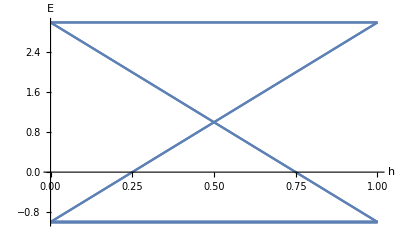

```mathematica
Plot[Energies/. x2-> x1, {x1,0,1},AxesLabel->{"h","E"}]
```

```mathematica
Emin = Min[Energies/.x1-> 0.5/.x2-> 0.5]
TensorMap = DeleteCases[Table[If[(Energy[values]/. x1-> 0.5 /.x2-> 0.5 )== Emin, values],{values, Tuples[Table[{-1,1},{i,1, ntot}]]}],Null]
```

-1

{{-1,-1,1,-1},{-1,-1,1,1},{-1,1,-1,1},{-1,1,1,-1},{-1,1,1,1},{1,-1,-1,-1},{1,-1,-1,1},{1,-1,1,-1},{1,1,-1,-1},{1,1,-1,1}}

```mathematica
NotebookDirectory[]
```

/home/jcolbois/ownCloud/Doctorat/Recherche/Dipolar Ising Model/Notes/TensorNetworks/TensorNetworksBases/ClassicalTNNotes/MFU/

```mathematica
Export[ToString[StringForm["``TLIAF_MFU.dat",NotebookDirectory[]]],TensorMap]
```

/home/jcolbois/ownCloud/Doctorat/Recherche/Dipolar Ising Model/Notes/TensorNetworks/TensorNetworksBases/ClassicalTNNotes/MFU/TLIAF_MFU.dat